# EOM of the Higgs in Palatini-Higgs preheating

```mathematica
(* useful everywhere *)
IntegrateByPart[expression_, derivative_, term_]:=
(*  term' = derivative *)
Module[{proptoderivative, integrated, result},
(* part proportional to the derivative to be eliminated. *)
proptoderivative =  Coefficient[expression, derivative];
(* integrated = U V' = - U' V *)
integrated =- D[proptoderivative,x] term;
result = expression - derivative proptoderivative + integrated;
(* remove 2nd order terms *)
result = result - Coefficient[result, term * derivative] * term * derivative;
Return[result]
]
(* expliciting the contractions *)
Format[D[f_[x,t],{t,n_/;n<3}]]:=OverDot[f,n][x,t];
Format[D[f_[t],{t,n_/;n<3}]]:=OverDot[f,n][t];
substterms = {
(q_)''[x]:> - a[t]^(-2 α) D[q[x,t],{t,2}]+a[t]^-2∇_{x}^2 q[x,t],
((q_)'[x])^2:>- a[t]^(-2 α) D[q[x,t],t]^2+a[t]^-2(∇_{x} q[x,t])^2,
((q_)'[x])((r_)'[x]):>- a[t]^(-2 α) D[q[x,t],t] D[r[x,t],t]+a[t]^-2(∇_{x} q[x,t])(∇_{x} r[x,t]),
a'[x] (q_)'[x]:> - a[t]^(-2α)D[a[t],t]D[q[x,t],t],
(q_)[x]:> q[x,t]/; Not[Or[MatchQ[q,a], MatchQ[q, a']]],
a[x]:> a[t],
D[a[x,t],t]:>a'[t] ,
D[a[x,t],{t,2}]:>a''[t] ,
D[a[x,t],x]:>0,
D[a[x,t],{x,2}]-> 0
};

pvals = {λ-> 10^-3,ξ-> 10^7};
```

## Starting from the unitary gauge

### Without the field transformation

```mathematica
(* Here we have the following lagrangian density *)
LUnitary[h_] :=a[x]^(3-α)( -1/2 1/(1+  ξ h^2)(D[h,x])^2 - 1/4 λ/((1+  ξ h^2)^2)h^4)
```

```mathematica
(* vary wrt to h *)
L2h = LUnitary[h[x]]  // Simplify;
L1h = LUnitary[h[x]+δh[x]] // Simplify;
```

```mathematica
Series[L1h,{δh[x],0,1}, {δh'[x],0,1}] -L2h
```

(-(a[x]^(3-α) h'[x] δh'[x])/(1+ξ h[x]^2)+O[δh'[x]]^2)+((a[x]^(3-α) (-λ h[x]^3+ξ h[x] h'[x]^2+ξ^2 h[x]^3 h'[x]^2))/((1+ξ h[x]^2)^3)+(2 ξ a[x]^(3-α) h[x] h'[x] δh'[x])/((1+ξ h[x]^2)^2)+O[δh'[x]]^2) δh[x]+O[δh[x]]^2

```mathematica
(* Expand at linear order in h and h' *)
deltah = Series[L1h, {δh[x], 0, 1}, {δh'[x], 0, 1}] - L2h // Expand;
(* if there is a term prop to δh'[x], take care of it: *)
deltah = IntegrateByPart[deltah, δh'[x], δh[x]];
Collect[deltah, δh[x]]
(* now δh should be the global factor (check below) *)
```

δh[x] (((3-α) a[x]^(2-α) a'[x] h'[x])/(1+ξ h[x]^2)-(2 ξ a[x]^(3-α) h[x] h'[x]^2)/((1+ξ h[x]^2)^2)+(a[x]^(3-α) (-λ h[x]^3+ξ h[x] h'[x]^2+ξ^2 h[x]^3 h'[x]^2))/((1+ξ h[x]^2)^3)+(a[x]^(3-α) h''[x])/(1+ξ h[x]^2))

```mathematica
(* if all good, extract the eom *)
eomh = Coefficient[deltah, δh[x]] // Expand;
eomh = eomh / Coefficient[eomh, h''[x]]  // FullSimplify // Expand;
eomh = h'[x]^2  Simplify[Coefficient[eomh,h'[x]^2]] + λ Coefficient[eomh,λ]+ h''[x] Simplify[Coefficient[eomh, h''[x]]]+a'[x] Simplify[Coefficient[eomh, a'[x]]]
```

-(λ h[x]^3)/((1+ξ h[x]^2)^2)-((-3+α) a'[x] h'[x])/a[x]-(ξ h[x] h'[x]^2)/(1+ξ h[x]^2)+h''[x]

```mathematica
eomhe = eomh //. substterms // First;
eomhe = eomhe / Coefficient[eomhe,D[h[x,t],{t,2}]] // FullSimplify;
eomher = eomhe /. {h[x,t]->h[x,t]/√ξ, D[h[x,t],{t,1}]->  D[h[x,t],{t,1}]/√ξ, D[h[x,t],{t,2}]->  D[h[x,t],{t,2}]/√ξ, D[h[x,t],{x,1}]->  D[h[x,t],{x,1}]/√ξ, D[h[x,t],{x,2}]->  D[h[x,t],{x,2}]/√ξ};
eomher = -eomher / Coefficient[eomher,D[h[x,t],{t,2}]] // FullSimplify
```

-(λ a[t]^(2 α) h[x,t]^3)/(ξ (1+h[x,t]^2)^2)+((-3+α) ȧ[t] ḣ[x,t])/a[t]+(h[x,t] (ḣ[x,t])^2)/(1+h[x,t]^2)-ḧ[x,t]+a[t]^(-2+2 α) (-(h[x,t] (h^(1,0)[x,t])^2)/(1+h[x,t]^2)+h^(2,0)[x,t])

```mathematica
(* substituting the field transformation must yield the canonical eom *)
htochisubst ={h[x]-> 1/(√ξ)Sinh[√ξ χ[x]],h'[x]-> D[1/(√ξ)Sinh[√ξ χ[x]],x],h''[x]-> D[1/(√ξ)Sinh[√ξ χ[x]],{x,2}] }; 
eomh /. htochisubst // Simplify;
% / Coefficient[%, χ''[x]] // Simplify;
(* explicit the contractions *)
% //. substterms;
eomhtoχ = % / Coefficient[%, D[χ[x,t],{t,2}]] // Simplify
```

(λ a[t]^(2 α) Sech[√ξ χ[x,t]]^2 Tanh[√ξ χ[x,t]]^3)/ξ^(3/2)-((-3+α) ȧ[t] χ̇[x,t])/a[t]+χ̈[x,t]-a[t]^(-2+2 α) χ^(2,0)[x,t]

```mathematica
(* Numerically integrate without Hubble friction to check that the field oscillates as expected *)
eomhtoχ = eomhtoχ /. {χ[x,t]-> χ[t], D[χ[x,t],{x,2}]-> 0,  D[χ[x,t],{t,2}]->  D[χ[t],{t,2}], α-> 0, D[a[t],t]-> 0};
eomhtoχrescaled = √ξ eomhtoχ /. {χ[t]-> χ[t]/√ξ, D[χ[t],{t,2}]-> D[χ[t],{t,2}] / √ξ} // Simplify
```

(λ Sech[χ[t]]^2 Tanh[χ[t]]^3)/ξ+χ̈[t]

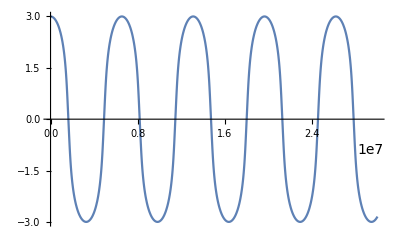

```mathematica
range = {t,0,3 10^7};
χini =3; 
sol = NDSolve[{eomhtoχrescaled ==0/. pvals, χ[0]==χini, χ'[0]==0}, χ[t], range];
Plot[χ[t] /. sol, range]
```

As expected: no slow roll since no hubble friction.

-(λ h[t]^3)/(ξ (1+h[t]^2)^2)+(h[t] (ḣ[t])^2)/(1+h[t]^2)-ḧ[t]

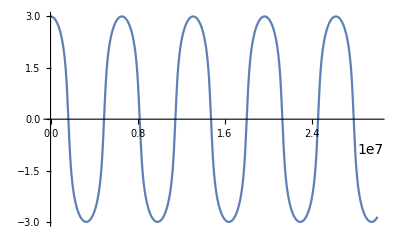

```mathematica
eomhToNum = eomh //. substterms // First;
eomhToNum = eomhToNum /.  {h[x,t]->h[t], D[h[x,t],{x,2}]-> 0,  D[h[x,t],{t,2}]->  D[h[t],{t,2}], α-> 0, D[a[t],t]-> 0,  D[h[x,t],{x,1}]-> 0, D[h[x,t],t]-> D[h[t],t]};
eomhToNum = eomhToNum // Simplify;
eomhToNumrescaled = √ξ eomhToNum/. {h[t]->h[t]/√ξ, D[h[t],{t,1}]-> D[h[t],{t,1}] / √ξ, D[h[t],{t,2}]-> D[h[t],{t,2}] / √ξ} // Simplify
hini =Sinh[χini];
solh = NDSolve[{eomhToNumrescaled ==0/. pvals, h[0]==hini, h'[0]==0}, h[t], range];
Plot[ArcSinh[h[t]] /. solh, range]
```

We obtain the exact same thing, so things check out until here.

### With the field transformation

```mathematica
Lχ2 = LUnitary[1/(√ξ)Sinh[√ξ χ[x]]] // FullSimplify
```

LUnitary[Sinh[√ξ χ[x]]/(√ξ)]

As expected, we get the tanh potential and a canonically normalized kinetic term.  Now perform the exact same procedure

```mathematica
toδh = D[1/(√ξ)Sinh[√ξ χ[x]], χ[x]] δχ[x];
Lχ1 = LUnitary[1/(√ξ)Sinh[√ξ χ[x]]+ toδh];
```

```mathematica
deltaχ = Series[Lχ1- Lχ2, {δχ[x],0,1}, {δχ'[x],0,1}];
(* if there is a term prop to δχ'[x], take care of it: *)
deltaχ = IntegrateByPart[deltaχ, δχ'[x], δχ[x]] // Simplify;
eomχ = Coefficient[deltaχ, δχ[x]] // Simplify;eomχ = eomχ / Coefficient[eomχ, χ''[x]] // Simplify
```

-(λ Sech[√ξ χ[x]]^2 Tanh[√ξ χ[x]]^3)/ξ^(3/2)-((-3+α) a'[x] χ'[x])/a[x]+χ''[x]

So ..the field transformed version gives the usual EOM without friction, as expected. 

Try the same but differently:

```mathematica
Lχ[χ_] := -(λ Tanh[√ξ χ]^4)/(4 ξ^2)-1/2 D[χ, x]^2
deltaχbis = Series[ Lχ[χ[x]+δχ[x]]- Lχ[χ[x]], {δχ[x],0,1},{δχ'[x],0,1}] // Expand;
δχ'[x] Coefficient[deltaχbis, δχ'[x]];
deltaχbis = IntegrateByPart[deltaχbis,  δχ'[x], δχ[x]];
Coefficient[%, δχ[x]] // Simplify
```

-(λ Sech[√ξ χ[x]]^2 Tanh[√ξ χ[x]]^3)/ξ^(3/2)+χ''[x]

## Simplified doublet: complex number

```mathematica
(* this is the lagrangian density. The volume element in the action only adds the Hubble friction, can be accounted for later. *)

RicciScalar = -6 a[x]^(-2-2α)((1-α)D[a[x],x]^2+a [x]D[a[x], {x,2}]);
L[H_] :=a[x]^(3-α) ((Mp^2+2ξ Conjugate[H] H)/2 RicciScalar -Conjugate[D[H,x]]D[H,x]-λ(Conjugate[H] H)^2 )
L[H_] :=a[x]^(3-α) (- 1/(1+ 2 ξ Conjugate[H] H)Conjugate[D[H,x]] D[H,x] - λ/(1+ 2 ξ Conjugate[H] H)^2(Conjugate[H] H)^2)
```

### H = ϕ1 + i ϕ2, use ϕ1 and ϕ2 as variables.

#### ϕ1

```mathematica
(* ϕ1 and ϕ2 are real scalars *)
$Assumptions = Element[ϕ1[x], Reals] && Element[ϕ2[x], Reals] &&Element[ϕ1'[x], Reals] && Element[ϕ2'[x], Reals] &&Element[δϕ1[x], Reals] && Element[δϕ1'[x], Reals] && Element[δϕ2[x], Reals] && Element[δϕ2'[x], Reals];
(* vary wrt to ϕ1 *)
L2ϕ = L[1/(√2)(ϕ1[x] + I ϕ2[x])]  // Simplify;
L1ϕ = L[1/(√2)(ϕ1[x]+ δϕ1[x] + I ϕ2[x])] // Simplify;
```

```mathematica
(* Expand at linear order in ϕ1 and ϕ1' *)
deltaϕ = Series[L1ϕ, {δϕ1[x], 0, 1}, {δϕ1'[x], 0, 1}] - L2ϕ // Expand;
(* if there is a term prop to δϕ1'[x], take care of it: *)
deltaϕ = IntegrateByPart[deltaϕ, δϕ1'[x], δϕ1[x]]
(* now δϕ1 should be the global factor (check below) *)
```

O[δϕ1'[x]]^2+((((3-α) a[x]^(2-α) a'[x] ϕ1'[x])/(1+ξ ϕ1[x]^2+ξ ϕ2[x]^2)-(a[x]^(3-α) ϕ1'[x] (2 ξ ϕ1[x] ϕ1'[x]+2 ξ ϕ2[x] ϕ2'[x]))/((1+ξ ϕ1[x]^2+ξ ϕ2[x]^2)^2)+(a[x]^(3-α) ϕ1[x] (-λ ϕ1[x]^2-λ ϕ2[x]^2+ξ ϕ1'[x]^2+ξ^2 ϕ1[x]^2 ϕ1'[x]^2+ξ^2 ϕ2[x]^2 ϕ1'[x]^2+ξ ϕ2'[x]^2+ξ^2 ϕ1[x]^2 ϕ2'[x]^2+ξ^2 ϕ2[x]^2 ϕ2'[x]^2))/((1+ξ ϕ1[x]^2+ξ ϕ2[x]^2)^3)+(a[x]^(3-α) ϕ1''[x])/(1+ξ ϕ1[x]^2+ξ ϕ2[x]^2))+O[δϕ1'[x]]^2) δϕ1[x]+O[δϕ1[x]]^2

```mathematica
(* if all good, extract the eom *)
eomϕ = Coefficient[deltaϕ, δϕ1[x]] // Expand;
eomϕ = eomϕ / Coefficient[eomϕ, ϕ1''[x]]  // FullSimplify
```

-((-3+α) a'[x] ϕ1'[x])/a[x]+1/((1+ξ (ϕ1[x]^2+ϕ2[x]^2))^2)(ϕ1[x] (-λ ϕ2[x]^2-ξ (1+ξ ϕ2[x]^2) ϕ1'[x]^2+ξ (1+ξ ϕ2[x]^2) ϕ2'[x]^2)-ϕ1[x]^3 (λ+ξ^2 (ϕ1'[x]^2-ϕ2'[x]^2))+ξ^2 ϕ1[x]^4 ϕ1''[x]+(1+ξ ϕ2[x]^2) (-2 ξ ϕ2[x] ϕ1'[x] ϕ2'[x]+(1+ξ ϕ2[x]^2) ϕ1''[x])+2 ξ ϕ1[x]^2 (-ξ ϕ2[x] ϕ1'[x] ϕ2'[x]+(1+ξ ϕ2[x]^2) ϕ1''[x]))

```mathematica
eomϕ // Expand;
Collect[%, {λ, a'[x], ϕ1''[x]}, Simplify]
```

-(λ ϕ1[x] (ϕ1[x]^2+ϕ2[x]^2))/((1+ξ ϕ1[x]^2+ξ ϕ2[x]^2)^2)-((-3+α) a'[x] ϕ1'[x])/a[x]+(ξ (-2 ϕ2[x] ϕ1'[x] ϕ2'[x]+ϕ1[x] (-ϕ1'[x]^2+ϕ2'[x]^2)))/(1+ξ ϕ1[x]^2+ξ ϕ2[x]^2)+ϕ1''[x]

```mathematica
(* try to fix the unitary gauge by neglecting one of the components *)
eomϕs = eomϕ /. {ϕ2[x]->0, ϕ2'[x]->0, ϕ1[x]->ϕ1[x], ϕ1'[x]-> ϕ1'[x],ϕ1''[x]-> ϕ1''[x]};
cϕ        = Coefficient[eomϕs, ϕ1''[x] ];
eomϕs = eomϕs  /cϕ  // FullSimplify // Expand
```

-(λ ϕ1[x]^3)/((1+ξ ϕ1[x]^2)^2)+(3 a'[x] ϕ1'[x])/a[x]-(α a'[x] ϕ1'[x])/a[x]-(ξ ϕ1[x] ϕ1'[x]^2)/((1+ξ ϕ1[x]^2)^2)-(ξ^2 ϕ1[x]^3 ϕ1'[x]^2)/((1+ξ ϕ1[x]^2)^2)+ϕ1''[x]

```mathematica
(* all good, just go term by term now *)
dpotϕ = λ Coefficient[eomϕs, λ];
frictionϕ =  ϕ1'[x]^2 Coefficient[eomϕs,  ϕ1'[x]^2] // FullSimplify;
boxϕ = ϕ1''[x] Coefficient[eomϕs, ϕ1''[x]];
(* add them back together *)
eomϕs = dpotϕ + frictionϕ + boxϕ;
(* display *)
boxϕ ==- frictionϕ -dpotϕ
(* the sign may appear wrong to be wrong, but will be corrected once the metric is explicited (-+++ signature). *)
```

ϕ1''[x]==(λ ϕ1[x]^3)/((1+ξ ϕ1[x]^2)^2)+(ξ ϕ1[x] ϕ1'[x]^2)/(1+ξ ϕ1[x]^2)

#### ϕ2

```mathematica
(* vary wrt to ϕ1 *)
L2ϕ2 = L[ϕ1[x] + I ϕ2[x]]  // Simplify;
L1ϕ2 = L[ϕ1[x] + I (ϕ2[x] + δϕ2[x])] // Simplify;
```

```mathematica
(* Expand at linear order in ϕ1 and ϕ1' *)
deltaϕ2 = Series[L1ϕ2, {δϕ2[x], 0, 1}, {δϕ2'[x], 0, 1}] - L2ϕ2 // Expand;
(* if there is a term prop to δϕ2'[x], take care of it: *)
deltaϕ2 = IntegrateByPart[deltaϕ2, δϕ2'[x], δϕ2[x]]
(* now δϕ2 should be the global factor (check below) *)
```

O[δϕ2'[x]]^2+(((2 (3-α) a[x]^(2-α) a'[x] ϕ2'[x])/(1+2 ξ ϕ1[x]^2+2 ξ ϕ2[x]^2)-(2 a[x]^(3-α) ϕ2'[x] (4 ξ ϕ1[x] ϕ1'[x]+4 ξ ϕ2[x] ϕ2'[x]))/((1+2 ξ ϕ1[x]^2+2 ξ ϕ2[x]^2)^2)+(4 a[x]^(3-α) ϕ2[x] (-λ ϕ1[x]^2-λ ϕ2[x]^2+ξ ϕ1'[x]^2+2 ξ^2 ϕ1[x]^2 ϕ1'[x]^2+2 ξ^2 ϕ2[x]^2 ϕ1'[x]^2+ξ ϕ2'[x]^2+2 ξ^2 ϕ1[x]^2 ϕ2'[x]^2+2 ξ^2 ϕ2[x]^2 ϕ2'[x]^2))/((1+2 ξ ϕ1[x]^2+2 ξ ϕ2[x]^2)^3)+(2 a[x]^(3-α) ϕ2''[x])/(1+2 ξ ϕ1[x]^2+2 ξ ϕ2[x]^2))+O[δϕ2'[x]]^2) δϕ2[x]+O[δϕ2[x]]^2

```mathematica
(* if all good, extract the eom *)
eomϕ2 = Coefficient[deltaϕ2, δϕ2[x]] // Expand;
eomϕ2 = eomϕ2 / Coefficient[eomϕ2, ϕ2''[x]]  // FullSimplify
```

-((-3+α) a'[x] ϕ2'[x])/a[x]+(2 ϕ2[x] (ξ ϕ1'[x]^2-(ϕ1[x]^2+ϕ2[x]^2) (λ-2 ξ^2 ϕ1'[x]^2))-4 ξ ϕ1[x] (1+2 ξ (ϕ1[x]^2+ϕ2[x]^2)) ϕ1'[x] ϕ2'[x]-2 ξ ϕ2[x] (1+2 ξ (ϕ1[x]^2+ϕ2[x]^2)) ϕ2'[x]^2)/((1+2 ξ (ϕ1[x]^2+ϕ2[x]^2))^2)+ϕ2''[x]

```mathematica
(* try to fix the unitary gauge by neglecting one of the components *)
eomϕ2s = eomϕ2 /. {ϕ1[x]->0, ϕ1'[x]->0, ϕ2[x]-> 1/(√2)ϕ2[x], ϕ2'[x]-> 1/(√2)ϕ2'[x] ,ϕ2''[x]-> 1/(√2)ϕ2''[x]};
cϕ2        = Coefficient[eomϕ2s, ϕ2''[x] ];
eomϕ2s = eomϕ2s  /cϕ2  // FullSimplify // Expand
```

-(λ ϕ2[x]^3)/((1+ξ ϕ2[x]^2)^2)+(3 a'[x] ϕ2'[x])/a[x]-(α a'[x] ϕ2'[x])/a[x]-(ξ ϕ2[x] ϕ2'[x]^2)/((1+ξ ϕ2[x]^2)^2)-(ξ^2 ϕ2[x]^3 ϕ2'[x]^2)/((1+ξ ϕ2[x]^2)^2)+ϕ2''[x]

```mathematica
(* all good, just go term by term now *)
dpotϕ2 = λ Coefficient[eomϕ2s, λ];
frictionϕ2 =  ϕ2'[x]^2 Coefficient[eomϕ2s,  ϕ2'[x]^2] // FullSimplify;
boxϕ2 = ϕ2''[x] Coefficient[eomϕ2s, ϕ2''[x]];
(* add them back together *)
eomϕ2s = dpotϕ2 + frictionϕ2 + boxϕ2;
(* display *)
boxϕ2 ==- frictionϕ2 -dpotϕ2
(* the sign may appear wrong to be wrong, but will be corrected once the metric is explicited (-+++ signature). *)
```

ϕ2''[x]==(λ ϕ2[x]^3)/((1+ξ ϕ2[x]^2)^2)+(ξ ϕ2[x] ϕ2'[x]^2)/(1+ξ ϕ2[x]^2)

Comparing the EOMs for ϕ1 and ϕ2:

```mathematica
eomϕ2 // FullSimplify
eomϕ// FullSimplify
```

-((-3+α) a'[x] ϕ2'[x])/a[x]+(2 ϕ2[x] (ξ ϕ1'[x]^2-(ϕ1[x]^2+ϕ2[x]^2) (λ-2 ξ^2 ϕ1'[x]^2))-4 ξ ϕ1[x] (1+2 ξ (ϕ1[x]^2+ϕ2[x]^2)) ϕ1'[x] ϕ2'[x]-2 ξ ϕ2[x] (1+2 ξ (ϕ1[x]^2+ϕ2[x]^2)) ϕ2'[x]^2)/((1+2 ξ (ϕ1[x]^2+ϕ2[x]^2))^2)+ϕ2''[x]

-((-3+α) a'[x] ϕ1'[x])/a[x]+1/((1+2 ξ (ϕ1[x]^2+ϕ2[x]^2))^2)(-2 λ ϕ1[x] (ϕ1[x]^2+ϕ2[x]^2)-2 ξ ϕ1[x] (1+2 ξ (ϕ1[x]^2+ϕ2[x]^2)) ϕ1'[x]^2-4 ξ ϕ2[x] (1+2 ξ (ϕ1[x]^2+ϕ2[x]^2)) ϕ1'[x] ϕ2'[x]+2 ξ ϕ1[x] (1+2 ξ (ϕ1[x]^2+ϕ2[x]^2)) ϕ2'[x]^2)+ϕ1''[x]

```mathematica
eomϕe = eomϕ //. substterms // First;
eomϕe = eomϕe a[t]^(2α)// FullSimplify
```

-(2 λ a[t]^(2 α) ϕ1[x,t] (ϕ1[x,t]^2+ϕ2[x,t]^2))/((1+2 ξ (ϕ1[x,t]^2+ϕ2[x,t]^2))^2)+((-3+α) ȧ[t] OverDot[ϕ1][x,t])/a[t]+(2 ξ (2 ϕ2[x,t] OverDot[ϕ1][x,t] OverDot[ϕ2][x,t]+ϕ1[x,t] ((OverDot[ϕ1][x,t])^2-(OverDot[ϕ2][x,t])^2)))/(1+2 ξ (ϕ1[x,t]^2+ϕ2[x,t]^2))-OverDoubleDot[ϕ1][x,t]+a[t]^(-2+2 α) (-(2 ξ (2 ϕ2[x,t] ϕ1^(1,0)[x,t] ϕ2^(1,0)[x,t]+ϕ1[x,t] ((ϕ1^(1,0)[x,t])^2-(ϕ2^(1,0)[x,t])^2)))/(1+2 ξ (ϕ1[x,t]^2+ϕ2[x,t]^2))+ϕ1^(2,0)[x,t])

```mathematica
eomϕe /. {ϕ1[x,t]^2+ϕ2[x,t]^2-> Φ^2}
```

-(2 λ Φ^2 a[t]^(2 α) ϕ1[x,t])/((1+2 ξ Φ^2)^2)+((-3+α) ȧ[t] OverDot[ϕ1][x,t])/a[t]+(2 ξ (2 ϕ2[x,t] OverDot[ϕ1][x,t] OverDot[ϕ2][x,t]+ϕ1[x,t] ((OverDot[ϕ1][x,t])^2-(OverDot[ϕ2][x,t])^2)))/(1+2 ξ Φ^2)-OverDoubleDot[ϕ1][x,t]+a[t]^(-2+2 α) (-(2 ξ (2 ϕ2[x,t] ϕ1^(1,0)[x,t] ϕ2^(1,0)[x,t]+ϕ1[x,t] ((ϕ1^(1,0)[x,t])^2-(ϕ2^(1,0)[x,t])^2)))/(1+2 ξ Φ^2)+ϕ1^(2,0)[x,t])

```mathematica
eomϕ2e = eomϕ2 //. substterms // First;
eomϕ2e = eomϕ2e a[t]^(2α)// FullSimplify
```

-(2 λ a[t]^(2 α) ϕ2[x,t] (ϕ1[x,t]^2+ϕ2[x,t]^2))/((1+2 ξ (ϕ1[x,t]^2+ϕ2[x,t]^2))^2)+((-3+α) ȧ[t] OverDot[ϕ2][x,t])/a[t]+(2 ξ (2 ϕ1[x,t] OverDot[ϕ1][x,t] OverDot[ϕ2][x,t]+ϕ2[x,t] (-(OverDot[ϕ1][x,t])^2+(OverDot[ϕ2][x,t])^2)))/(1+2 ξ (ϕ1[x,t]^2+ϕ2[x,t]^2))-OverDoubleDot[ϕ2][x,t]+a[t]^(-2+2 α) ((2 ξ (-2 ϕ1[x,t] ϕ1^(1,0)[x,t] ϕ2^(1,0)[x,t]+ϕ2[x,t] ((ϕ1^(1,0)[x,t])^2-(ϕ2^(1,0)[x,t])^2)))/(1+2 ξ (ϕ1[x,t]^2+ϕ2[x,t]^2))+ϕ2^(2,0)[x,t])

```mathematica
eomϕe /. {ϕ1[x,t]^2+ϕ2[x,t]^2-> Φ^2}
eomϕ2e /. {ϕ1[x,t]^2+ϕ2[x,t]^2-> Φ^2}
```

-(2 λ Φ^2 a[t]^(2 α) ϕ1[x,t])/((1+2 ξ Φ^2)^2)+((-3+α) ȧ[t] OverDot[ϕ1][x,t])/a[t]+(2 ξ (2 ϕ2[x,t] OverDot[ϕ1][x,t] OverDot[ϕ2][x,t]+ϕ1[x,t] ((OverDot[ϕ1][x,t])^2-(OverDot[ϕ2][x,t])^2)))/(1+2 ξ Φ^2)-OverDoubleDot[ϕ1][x,t]+a[t]^(-2+2 α) (-(2 ξ (2 ϕ2[x,t] ϕ1^(1,0)[x,t] ϕ2^(1,0)[x,t]+ϕ1[x,t] ((ϕ1^(1,0)[x,t])^2-(ϕ2^(1,0)[x,t])^2)))/(1+2 ξ Φ^2)+ϕ1^(2,0)[x,t])

-(2 λ Φ^2 a[t]^(2 α) ϕ2[x,t])/((1+2 ξ Φ^2)^2)+((-3+α) ȧ[t] OverDot[ϕ2][x,t])/a[t]+(2 ξ (2 ϕ1[x,t] OverDot[ϕ1][x,t] OverDot[ϕ2][x,t]+ϕ2[x,t] (-(OverDot[ϕ1][x,t])^2+(OverDot[ϕ2][x,t])^2)))/(1+2 ξ Φ^2)-OverDoubleDot[ϕ2][x,t]+a[t]^(-2+2 α) ((2 ξ (-2 ϕ1[x,t] ϕ1^(1,0)[x,t] ϕ2^(1,0)[x,t]+ϕ2[x,t] ((ϕ1^(1,0)[x,t])^2-(ϕ2^(1,0)[x,t])^2)))/(1+2 ξ Φ^2)+ϕ2^(2,0)[x,t])

### Use H = ρ e^iϕ as variables

#### ρ

```mathematica
(* ρ and ϕ are real scalars *)
$Assumptions = Element[ϕ[x], Reals] && Element[ρ[x], Reals] && ρ[x]> 0&&Element[ϕ'[x], Reals] && Element[ρ'[x], Reals] &&Element[δϕ[x], Reals] && Element[δϕ'[x], Reals] && Element[δρ[x], Reals] && Element[δρ'[x], Reals];
(* vary wrt to ρ *)
L2ρ = L[ρ[x]Exp[I ϕ[x]]]  // Simplify;
L1ρ = L[(ρ[x]+δρ[x])Exp[I ϕ[x]]] // Simplify;
```

```mathematica
(* Expand at linear order in ϕ1 and ϕ1' *)
deltaρ = Series[L1ρ, {δρ[x], 0, 1}, {δρ'[x], 0, 1}] - L2ρ // Expand;
(* if there is a term prop to δϕ1'[x], take care of it: *)
deltaρ = IntegrateByPart[deltaρ, δρ'[x], δρ[x]]
(* now δϕ1 should be the global factor (check below) *)
```

O[δρ'[x]]^2+(((2 (3-α) a[x]^(2-α) a'[x] ρ'[x])/(1+2 ξ ρ[x]^2)-(8 ξ a[x]^(3-α) ρ[x] ρ'[x]^2)/((1+2 ξ ρ[x]^2)^2)+(2 a[x]^(3-α) ρ[x] (-2 λ ρ[x]^2+2 ξ ρ'[x]^2+4 ξ^2 ρ[x]^2 ρ'[x]^2-ϕ'[x]^2-2 ξ ρ[x]^2 ϕ'[x]^2))/((1+2 ξ ρ[x]^2)^3)+(2 a[x]^(3-α) ρ''[x])/(1+2 ξ ρ[x]^2))+O[δρ'[x]]^2) δρ[x]+O[δρ[x]]^2

```mathematica
(* if all good, extract the eom *)
eomρ = Coefficient[deltaρ, δρ[x]] // Expand;
eomρ = eomρ / Coefficient[eomρ, ρ''[x]]  // FullSimplify
```

-((-3+α) a'[x] ρ'[x])/a[x]-(ρ[x] (2 ξ ρ'[x]^2+ϕ'[x]^2+2 ρ[x]^2 (λ+ξ (2 ξ ρ'[x]^2+ϕ'[x]^2))))/((1+2 ξ ρ[x]^2)^2)+ρ''[x]

```mathematica
(* try to fix the unitary gauge by setting ϕ->0 *)
eomρs = eomρ /. {ϕ[x]->0,ϕ'[x]->0};
cρ        = Coefficient[eomρs,ρ''[x] ];
eomρs = eomρs  /cρ  // FullSimplify // Expand
```

-(2 λ ρ[x]^3)/((1+2 ξ ρ[x]^2)^2)+(3 a'[x] ρ'[x])/a[x]-(α a'[x] ρ'[x])/a[x]-(2 ξ ρ[x] ρ'[x]^2)/((1+2 ξ ρ[x]^2)^2)-(4 ξ^2 ρ[x]^3 ρ'[x]^2)/((1+2 ξ ρ[x]^2)^2)+ρ''[x]

```mathematica
(* all good, just go term by term now *)
dpotρ = λ Coefficient[eomρs, λ];
frictionρ =  ρ'[x]^2 Coefficient[eomρs,  ρ'[x]^2] // FullSimplify;
boxρ = ρ''[x] Coefficient[eomρs, ρ''[x]];
Hubbleρ =a'[x] Simplify[ Coefficient[eomρs, a'[x]]];
(* add them back together *)
eomρs = dpotρ + frictionρ+ boxρ+Hubbleρ;
(* display *)
boxρ ==- frictionρ -dpotρ-Hubbleρ
(* the sign may appear wrong to be wrong, but will be corrected once the metric is explicited (-+++ signature). *)
```

ρ''[x]==(2 λ ρ[x]^3)/((1+2 ξ ρ[x]^2)^2)+((-3+α) a'[x] ρ'[x])/a[x]+(2 ξ ρ[x] ρ'[x]^2)/(1+2 ξ ρ[x]^2)

```mathematica
(* explicit the derivatives *)
eomρe = eomρ/. {a[x]-> a[t], a'[x]-> a'[t], ρ[x]-> ρ[x,t], ρ'[x]-> ρ'[x,t],ρ''[x]-> ρ''[x,t], ϕ'[x]-> ϕ'[x,t], ϕ''[x]-> ϕ''[x,t]} // Expand;
eomρe = eomρe //. {t1_'[t] t2_'[x,t]-> -a[t]^(-2α) D[t1[t],t] D[t2[x,t],t]};
eomρe = eomρe //.  {t1_'[x,t] t2_'[x,t]-> -a[t]^(-2α) D[t1[x,t],t] D[t2[x,t],t]+a[t]^-2 D[t1[x,t],x]D[t2[x,t],x], ρ''[x,t]-> -a[t]^(-2α)D[ρ[x,t],{t,2}]+a[t]^-2 D[ρ[x,t],{x,2}]};
eomρe = eomρe //. {t1_'[x,t]^2-> -a[t]^(-2α) D[t1[x,t],t]^2 +a[t]^-2 D[t1[x,t],x]^2};
eomρe = eomρe/ Coefficient[eomρe, D[ρ[x,t], {t,2}]] // FullSimplify
(*eomρe /. {ρ[x,t] -> ρ[t] Exp[-I k x]}*)
```

(2 λ a[t]^(2 α) ρ[x,t]^3)/((1+2 ξ ρ[x,t]^2)^2)-((-3+α) ȧ[t] ρ̇[x,t])/a[t]-(ρ[x,t] (2 ξ (ρ̇[x,t])^2+(ϕ̇[x,t])^2))/(1+2 ξ ρ[x,t]^2)+ρ̈[x,t]+a[t]^(-2+2 α) ((ρ[x,t] (2 ξ (ρ^(1,0)[x,t])^2+(ϕ^(1,0)[x,t])^2))/(1+2 ξ ρ[x,t]^2)-ρ^(2,0)[x,t])

```mathematica
eomρelin = eomρe /. {
ρ[x,t]-> ρ[t]+δρ[x,t],
(*
D[ρ[x,t],x]-> D[ρ[t]+δρ[t]Exp[ I k x],x],
D[ρ[x,t],t]-> D[ρ[t]+δρ[t] Exp[ I k x],t],
D[ρ[x,t], {x,2}]-> D[ρ[t]+δρ[t] Exp[ I k x],{x,2}],
D[ρ[x,t], {t,2}]-> D[ρ[t]+δρ[t] Exp[ I k x],{t,2}],
*)
D[ρ[x,t],x]-> D[ρ[t]+δρ[x,t],x],
D[ρ[x,t],t]-> D[ρ[t]+δρ[x,t],t],
D[ρ[x,t], {x,2}]-> D[ρ[t]+δρ[x,t],{x,2}],
D[ρ[x,t], {t,2}]-> D[ρ[t]+δρ[x,t],{t,2}],
D[ϕ[x,t],x]-> 0,
D[ϕ[x,t],t]-> 0
};
```

#### ϕ

```mathematica
(* ρ and ϕ are real scalars *)
$Assumptions = Element[ϕ[x], Reals] && Element[ρ[x], Reals] &&Element[ϕ'[x], Reals] && Element[ρ'[x], Reals] &&Element[δϕ[x], Reals] && Element[δϕ'[x], Reals] && Element[δρ[x], Reals] && Element[δρ'[x], Reals];
(* vary wrt to ϕ *)
L2phase = L[ρ[x]Exp[I ϕ[x]]]  // Simplify;
L1phase= L[ρ[x]Exp[I ϕ[x]+I δϕ[x]]] // Simplify;
```

```mathematica
(* Expand at linear order in ϕ1 and ϕ1' *)
deltaphase = Series[L1phase, {δϕ[x], 0, 1}, {δϕ'[x], 0, 1}] - L2phase // Expand;
(* if there is a term prop to δϕ1'[x], take care of it: *)
deltaphase = IntegrateByPart[deltaphase, δϕ'[x], δϕ[x]]
(* now δϕ should be the global factor (check below) *)
```

1/((1+2 ξ ρ[x]^2)^2)2 a[x]^(2-α) δϕ[x] ρ[x] (3 ρ[x] a'[x] ϕ'[x]-α ρ[x] a'[x] ϕ'[x]+6 ξ ρ[x]^3 a'[x] ϕ'[x]-2 α ξ ρ[x]^3 a'[x] ϕ'[x]+2 a[x] ρ'[x] ϕ'[x]+a[x] ρ[x] ϕ''[x]+2 ξ a[x] ρ[x]^3 ϕ''[x])+O[δϕ'[x]]^2

```mathematica
(* if all good, extract the eom *)
eomphase = Coefficient[deltaphase, δϕ[x]] // Expand;
eomphase = eomphase / Coefficient[eomphase, ϕ''[x]]  // FullSimplify
```

(-((-3+α) a'[x])/a[x]+(2 ρ'[x])/(ρ[x]+2 ξ ρ[x]^3)) ϕ'[x]+ϕ''[x]

Now let’s take ρ as a background variable (we know it will oscillate consistently at the beginning; and its perturbations will grow dramatically). That is expand ϕ around its average value: ϕ[x,t]-> ϕ[t] + δϕ[x,t] and go order by order. 
We also know that ρ[x,t] will be relatively homogeneous at the beginning: ρ[x,t]-> ρ[t]+δρ[t] Exp[- I k_Tx]. The gradient of ρ[x,t] can also be expanded around the value that we know grows: k_T for the tachyonic modes.  ρ[t] and δρ[t] are known.

```mathematica
(* explicit the derivatives *)
eomphasee = eomphase/. {a[x]-> a[t], a'[x]-> a'[t], ρ[x]-> ρ[x,t], ρ'[x]-> ρ'[x,t], ϕ'[x]-> ϕ'[x,t], ϕ''[x]-> ϕ''[x,t]} // Expand;
eomphasee = eomphasee //. {t1_'[t] t2_'[x,t]-> -a[t]^(-2α) D[t1[t],t] D[t2[x,t],t]};
eomphasee = eomphasee //.  {t1_'[x,t] t2_'[x,t]-> -a[t]^(-2α) D[t1[x,t],t] D[t2[x,t],t]+a[t]^-2 D[t1[x,t],x]D[t2[x,t],x], ϕ''[x,t]-> -a[t]^(-2α)D[ϕ[x,t],{t,2}]+a[t]^-2 D[ϕ[x,t],{x,2}]};
δeomphasee =eomphasee //. {
D[ϕ[x,t],t]-> Hold[ D[ϕ[t]+δϕ[x,t],t]],
D[ϕ[x,t],x]->  Hold[D[δϕ[x,t],x]],
 D[ϕ[x,t],{x,2}]->  Hold[D[δϕ[x,t],{x,2}]], 
D[ϕ[x,t],{t,2}]-> Hold[ D[ϕ[t]+δϕ[x,t],{t,2}]],
ρ[x,t]->ρ[t],(* neglect the perturbations around the average of ρ *)
D[ρ[x,t],t]->Hold[D[ρ[t],t]],
D[ρ[x,t],x]->Hold[D[δρ[t] Exp[-I Subscript[k, T] x],x]]
}// Expand;
eomphaseehom = eomphasee /.{
ρ[x,t]-> ρ[t],
D[ρ[x,t],t]-> D[ρ[t],t],
ϕ[x,t]-> ϕ[t],
D[ϕ[x,t],{t,n_}]-> D[ϕ[t],{t,n}],
D[ϕ[x,t],x]-> 0,
D[ϕ[x,t],{x,2}]-> 0
};
```

### Use H and H^* as variables.

```mathematica
(* vary wrt to H *)
L2H = L[H[x]]  // Simplify;
L1H = L[H[x]] // Simplify;
L1H = L1H /. {Conjugate[H[x]] -> SuperStar[H][x], Conjugate[H'[x]] -> (SuperStar[H])'[x]};
L2H = L2H /. {Conjugate[H[x]] -> SuperStar[H][x], Conjugate[H'[x]] -> (SuperStar[H])'[x]};
L1H = L1H /.{  SuperStar[H][x] ->  SuperStar[H][x] + SuperStar[δH][x],   (SuperStar[H])'[x] ->  (SuperStar[H])'[x] + (SuperStar[δH])'[x]}
```

a[x]^(3-α) (-λ H[x]^2 (H^*[x]+δH^*[x])^2-H'[x] ((H^*)'[x]+(δH^*)'[x])-3 a[x]^(-2 (1+α)) (Mp^2+2 ξ H[x] (H^*[x]+δH^*[x])) (-(-1+α) a'[x]^2+a[x] a''[x]))

```mathematica
(* Expand at linear order in H and H' *)
deltaH = Series[L1H, {SuperStar[δH][x], 0, 1},{(SuperStar[δH])'[x], 0, 1}] - L2H // Expand
(* if there is a term prop to δH*'[x], take care of it: *)
deltaH = IntegrateByPart[deltaH, (SuperStar[δH])'[x], SuperStar[δH][x]]
(* now δH* should be the global factor (check below) *)
```

(-a[x]^(3-α) H'[x] (δH^*)'[x]+O[(δH^*)'[x]]^2)+a[x]^(3-α) (-2 λ H[x]^2 H^*[x]-6 ξ a[x]^(-2 (1+α)) H[x] (-(-1+α) a'[x]^2+a[x] a''[x])) δH^*[x]+O[δH^*[x]]^2

O[(δH^*)'[x]]^2+((3-α) a[x]^(2-α) a'[x] H'[x]+a[x]^(3-α) (-2 λ H[x]^2 H^*[x]-6 ξ a[x]^(-2 (1+α)) H[x] (-(-1+α) a'[x]^2+a[x] a''[x]))+a[x]^(3-α) H''[x]) δH^*[x]+O[δH^*[x]]^2

```mathematica
(* if all good, extract the eom *)
eomH = Coefficient[deltaH, SuperStar[δH][x]] // Expand ;
(*    ((H')^*)' is (H^*)''  *)
(*eomH = eomH /. {((H')^*)'[x] -> (H^*)''[x], (H')^*[x]-> (H^*)'[x]};*)
eomH = eomH / Coefficient[eomH, H''[x]]  // FullSimplify
```

-2 λ H[x]^2 H^*[x]-((-3+α) a'[x] H'[x])/a[x]+6 ξ a[x]^(-2 (1+α)) H[x] ((-1+α) a'[x]^2-a[x] a''[x])+H''[x]

```mathematica
(* try to fix the unitary gauge by taking the norm of H *)
eomHs = eomH /. {H[x]->1/(√2) h[x],H'[x]->1/(√2) h'[x],(SuperStar[H])''[x]->1/(√2) h''[x],(SuperStar[H])'[x]->1/(√2) h'[x],SuperStar[(H')][x]-> 1/(√2)h'[x],SuperStar[H][x]-> 1/(√2)h[x],H''[x]->1/(√2) h''[x]};
cH        = Coefficient[eomHs, h''[x] ];
eomHs = eomHs  /cH  // FullSimplify // Expand
```

-λ h[x]^3-6 ξ a[x]^(-2 (1+α)) h[x] a'[x]^2+6 α ξ a[x]^(-2 (1+α)) h[x] a'[x]^2+(3 a'[x] h'[x])/a[x]-(α a'[x] h'[x])/a[x]-6 ξ a[x]^(1-2 (1+α)) h[x] a''[x]+h''[x]

```mathematica
(* all good, just go term by term now *)
dpotH = λ Coefficient[eomHs, λ];
frictionH =  h'[x]^2 Coefficient[eomHs,  h'[x]^2] // FullSimplify;
boxH = h''[x] Coefficient[eomHs, h''[x]];
HubbleH =a'[x] Simplify[ Coefficient[eomHs, a'[x]]];
(* add them back together *)
eomHs = dpotH + frictionH + boxH + HubbleH;
(* display *)
boxH==- frictionH -dpotH -HubbleH
(* the sign may appear wrong to be wrong, but will be corrected once the metric is explicited (-+++ signature). *)
```

h''[x]==λ h[x]^3+((-3+α) a'[x] h'[x])/a[x]

#### Explicit the derivatives and the metric

```mathematica
eomHe = (eomH //. substterms) // First;
eomHe = eomHe a[t]^(2α)// Expand;
rescaling = {
D[H[x,t],{t,2}]-> D[H[x,t],{t,2}] /√ξ, 
D[SuperStar[H][x,t],{t,2}]-> D[SuperStar[H][x,t],{t,2}] /√ξ,
D[H[x,t],t]-> D[H[x,t],t] /√ξ,
D[SuperStar[H][x,t],t]-> D[SuperStar[H][x,t],t] /√ξ,  
D[H[x,t],{x,2}]-> D[H[x,t],{x,2}] /√ξ,
D[SuperStar[H][x,t],{x,2}]-> D[SuperStar[H][x,t],{x,2}] /√ξ,
D[H[x,t],x]-> D[H[x,t],x] /√ξ,  
D[SuperStar[H][x,t],x]-> D[SuperStar[H][x,t],x] /√ξ,
H[x,t]:> H[x,t] /√ξ,
SuperStar[H][x,t]-> SuperStar[H][x,t]/√ξ
};
rescaling = {
D[H[x,t],{t,2}]-> D[H[x,t],{t,2}]  ((√λ)/(2ξ))^2, 
D[SuperStar[H][x,t],{t,2}]-> D[SuperStar[H][x,t],{t,2}] ((√λ)/(2ξ))^2,
D[H[x,t],t]-> D[H[x,t],t] ((√λ)/(2ξ)),
D[SuperStar[H][x,t],t]-> D[SuperStar[H][x,t],t] ((√λ)/(2ξ)),  
D[H[x,t],{x,2}]-> D[H[x,t],{x,2}]((√λ)/(2ξ))^2,
D[SuperStar[H][x,t],{x,2}]-> D[SuperStar[H][x,t],{x,2}]((√λ)/(2ξ))^2,
D[H[x,t],x]-> D[H[x,t],x] ((√λ)/(2ξ)),  
D[SuperStar[H][x,t],x]-> D[SuperStar[H][x,t],x] ((√λ)/(2ξ)),
D[a[t],t]-> D[a[t],t] ((√λ)/(2ξ)),
H[x,t]:> H[x,t],
SuperStar[H][x,t]-> SuperStar[H][x,t]
};
eomHe = eomHe /. rescaling //Expand ; 
eomHe = eomHe / Coefficient[eomHe, D[H[x,t],{t,2}]] // Expand;
eomHe = Collect[-eomHe, {a'[t], a[t]^(-2+2α),D[H[x,t],{t,2}], a[t]^(2α)}, FullSimplify]
```

-8 ξ^2 a[t]^(2 α) H[x,t]^2 H^*[x,t]-6 (-1+α) ξ a[t]^(-2-2 α) H[x,t] (ȧ[t])^2+(24 ξ^3 a[t]^(-1-2 α) H[x,t] ä[t])/λ+((-3+α) ȧ[t] Ḣ[x,t])/a[t]-Ḧ[x,t]+a[t]^(-2+2 α) H^(2,0)[x,t]

```mathematica
eomHeLyx = -Derivative[0,2][H][x,t] + a[t]^(-2(1-α))Derivative[2,0][H][x,t] - ((3-α) D[a[t],t] Derivative[0,1][H][x,t])/a[t] + (2 ξ  SuperStar[H][x,t])/(1+ 2 ξ  SuperStar[H][x,t]  H[x,t])((Derivative[0,1][H][x,t])^2 - a[t]^(-2(1-α)) (Derivative[1,0][H][x,t])^2)-(2 a[t]^(2α)λ SuperStar[H][x,t]  H[x,t]^2)/(1+ 2 ξ  SuperStar[H][x,t]  H[x,t])^2;
eomHeLyx = -Derivative[0,2][H][x,t] + a[t]^(-2(1-α))Derivative[2,0][H][x,t] - ((3-α) D[a[t],t] Derivative[0,1][H][x,t])/a[t] + (2 ξ  SuperStar[H][x,t])/(1+ 2 ξ  SuperStar[H][x,t]  H[x,t])((Derivative[0,1][H][x,t])^2 - a[t]^(-2(1-α)) (Derivative[1,0][H][x,t])^2)-(8 a[t]^(2α)ξ^2 SuperStar[H][x,t]  H[x,t]^2)/(1+ 2 ξ  SuperStar[H][x,t]  H[x,t])^2;
```

```mathematica
eomHe-eomHeLyx // Expand  // Simplify
```

0

```mathematica
eomHe
```

(2 (-3+α) ξ ȧ[t] Ḣ[x,t])/(√λ a[t])+(2 ξ H^*[x,t] (-4 ξ a[t]^(2 α) H[x,t]^2+(1+2 ξ H[x,t] H^*[x,t]) (Ḣ[x,t])^2))/((1+2 ξ H[x,t] H^*[x,t])^2)-Ḧ[x,t]+a[t]^(-2+2 α) (-(2 ξ H^*[x,t] (H^(1,0)[x,t])^2)/(1+2 ξ H[x,t] H^*[x,t])+H^(2,0)[x,t])

Without the gradients for the initial tests:

```mathematica
eomHeNoGrad = eomHe /. {D[H[x,t],x]-> 0, D[H[x,t],{x,2}]-> 0}
```

((-3+α) ȧ[t] Ḣ[x,t])/a[t]+(2 H^*[x,t] (-λ a[t]^(2 α) H[x,t]^2+ξ (1+2 H[x,t] H^*[x,t]) (Ḣ[x,t])^2))/(ξ (1+2 H[x,t] H^*[x,t])^2)-Ḧ[x,t]

To find the fluctuations, could work to send H to 0+δH:

```mathematica
eomHeNoGrad /. {H[x,t]-> H+δH[t], SuperStar[H][x,t]->SuperStar[H]+ SuperStar[δH][t], D[H[x,t],t]-> D[δH[t],t], D[H[x,t],{t,2}]-> D[δH[t],{t,2}]};
Series[%, {δH[t],0,1}, {SuperStar[δH][t],0,1},{D[δH[t],t],0,1}]
```

(((-(2 H^2 λ a[t]^(2 α) H^*)/(ξ (1+2 H H^*)^2)-OverDoubleDot[δH][t])+((-3+α) ȧ[t] OverDot[δH][t])/a[t]+O[OverDot[δH][t]]^2)+((2 H^2 λ a[t]^(2 α) (-1+2 H H^*))/(ξ (1+2 H H^*)^3)+O[OverDot[δH][t]]^2) δH^*[t]+O[δH^*[t]]^2)+((-(4 (H λ a[t]^(2 α) H^*))/(ξ (1+2 H H^*)^3)+O[OverDot[δH][t]]^2)+((4 H λ a[t]^(2 α) (-1+4 H H^*))/(ξ (1+2 H H^*)^4)+O[OverDot[δH][t]]^2) δH^*[t]+O[δH^*[t]]^2) δH[t]+O[δH[t]]^2

#### EOM of the scale factor

```mathematica
L1 = L[H[x]] + a[x]^(3-α)(1/2 RicciScalar);
L1 = L1 /. {RicciScalar -> a[t]^(-2 (1+α)) (6 (-1+α) D[a[t],t]^2-6 a[t] D[a[t],{t,2}])};
L1 = L1/. {Conjugate[H[x]] -> SuperStar[H][x], Conjugate[H'[x]] -> SuperStar[H'][x]};
(* L1 = L1 /. {(H')^*[x] H'[x] -> (-a[t]^(-2α)D[H^*[x,t],t]D[H[x,t],t] + a[t]^-2 D[H^*[x,t],x]D[H[x,t],x]), a[x]-> a[t]}
L2 = L1 /. {a[t]-> a[t]+δa[t]}; *)
L1 = L1 //. {SuperStar[(H')][x] H'[x] -> (-a[t]^(-2α)D[SuperStar[H][x,t],t]D[H[x,t],t] ), a[x]-> a[t], H[x]-> H[x,t], SuperStar[H][x]-> SuperStar[H][x,t]};
L2 = L1 /. {a[t]-> a[t]+δa[t], a'[t]-> a'[t]+δa'[t],a''[t]-> a''[t]+δa''[t]};
deltaa = Series[L2 - L1, {δa[t],0,1},{δa'[t],0,1},{δa''[t],0,1}] // Simplify //Expand;
deltaa = IntegrateByPart[deltaa, δa''[t], δa'[t]] // Expand;
deltaa = IntegrateByPart[deltaa, δa'[t], δa[t]] // Expand
eoma = Coefficient[deltaa, δa[t]];
eoma = eoma / Coefficient[eoma, a''[t]] // Simplify
```

(O[δa''[t]]^2+O[δa'[t]]^2)+((1/2 a[t]^(-3 α) (-6 a[t] a''[t]+(-1+3 α) (-6 (-1+α) a'[t]^2+6 a[t] a''[t])-(4 α a[t]^2 Ḣ[x,t] OverDot[H^*][x,t])/(1+2 ξ H[x,t] H^*[x,t])+(2 (-3+α) a[t]^2 (λ a[t]^(2 α) H[x,t]^2 (H^*[x,t])^2-(1+2 ξ H[x,t] H^*[x,t]) Ḣ[x,t] OverDot[H^*][x,t]))/((1+2 ξ H[x,t] H^*[x,t])^2))+O[δa''[t]]^2)+(-6 (-1+α) (-1+3 α) a[t]^(-3 α) a'[t]+6 (1-4 α+3 α^2) a[t]^(-3 α) a'[t]) δa'[t]+O[δa'[t]]^2) δa[t]+O[δa[t]]^2

((-3+α) λ a[t]^(1+2 α) H[x,t]^2 (H^*[x,t])^2)/(3 (-2+3 α) (1+2 ξ H[x,t] H^*[x,t])^2)+((-1+4 α-3 α^2) a'[t]^2)/((-2+3 α) a[t])+a''[t]-((-1+α) a[t] Ḣ[x,t] OverDot[H^*][x,t])/((-2+3 α) (1+2 ξ H[x,t] H^*[x,t]))

```mathematica
eoma /. α-> 0;
% / a[t];
% /. {a'[t] -> Η[t]a[t]};
eomas = -% // Expand
```

-1/2 Η[t]^2-(λ H[x,t]^2 (H^*[x,t])^2)/(2 (1+2 ξ H[x,t] H^*[x,t])^2)-a''[t]/a[t]+(Ḣ[x,t] OverDot[H^*][x,t])/(2 (1+2 ξ H[x,t] H^*[x,t]))

### Checks

#### Potential term

```mathematica
(* we have the following "interaction" term: *)
dpoth = dpotH /. {h[x]-> h}
```

-(h^3 λ)/((1+h^2 ξ)^2)

```mathematica
(* take the Einstein frame potential in unitary gauge *)
pot =1/((1 +2ξ h^2)^2)   λ/4 h^4;
(* the derivative will give the above (modulo a factor that we multiplied the eom with, and a factor 2 that I cannot account for yet*)
-D[pot, h] // FullSimplify
```

-(h^3 λ)/((1+2 h^2 ξ)^3)

#### Substitute the field redefinition

```mathematica
(* re-introduce the factor we removed before *)
eom = eomHs   cH // Expand;
(* this is the value of h in function of χ *)
hofχ[x_] := 1/(√ξ)Sinh[√ξ χ[x]];
(* replace all occurences in the eom *)
eomχ = eom /. {h[x] -> hofχ[x], h'[x]-> D[hofχ[x],x], h''[x]-> D[hofχ[x],{x,2}]} // FullSimplify
```

(Cosh[√ξ χ[x]] (-(-3+α) ξ^(3/2) a'[x] χ'[x]+a[x] (-λ Sech[√ξ χ[x]]^2 Tanh[√ξ χ[x]]^3+ξ^(3/2) χ''[x])))/(√2 ξ^(3/2) a[x])

```mathematica
(* extract relevant part *)
eomχbis = eomχ / Coefficient[eomχ, χ''[x]] // Simplify
```

-(λ Sech[√ξ χ[x]]^2 Tanh[√ξ χ[x]]^3)/ξ^(3/2)-((-3+α) a'[x] χ'[x])/a[x]+χ''[x]

```mathematica
(* the part proportional to λ is indeed the derivative of the Palatini Einstein frame potential in terms of the redefined field *)
palatiniEinsteinFramePot=(λ Tanh[√ξ χ[x]]^4)/(4 ξ^2);
-D[palatiniEinsteinFramePot,χ[x]]-λ Coefficient[eomχbis, λ]
(* gives 0 *)
```

0

## Full SU2 doublet

```mathematica
L[H_] := - 1/(1+ 2 ξ ConjugateTranspose[H].H)ConjugateTranspose[D[H,x]].D[H,x] - λ/(1+ 2 ξ ConjugateTranspose[H].H)^2(ConjugateTranspose[H].H)^2
```

```mathematica
$Assumptions = {Element[{ξ1[x], ξ1'[x],δξ1[x],δξ1'[x],ξ2[x], ξ2'[x],ξ3[x], ξ3'[x],ξ4[x], ξ4'[x]}, Reals]};
SU2Doublet = {{ξ1[x] + I ξ2[x]},{ ξ3[x] + I ξ4[x]}} ;
δSU2Doublet =  {{δξ1[x]},{0}};
L1SU2 = L[SU2Doublet + δSU2Doublet];
L2SU2 = L [SU2Doublet];
```

```mathematica
(* Expand at linear order in ξ1 and ξ1' *)
deltaSU2 = Series[L1SU2, {δξ1[x], 0, 1}, {δξ1'[x], 0, 1}] - L2SU2 // Expand;
(* if there is a term prop to δϕ1'[x], take care of it: *)
deltaSU2 = IntegrateByPart[deltaSU2, δξ1'[x], δξ1[x]];
(* remove the 2nd order terms *)
deltaSU2 = deltaSU2 - Coefficient[deltaSU2, δξ1'[x] δξ1[x]] δξ1'[x] δξ1[x]
(* now δξ1 should be the global factor (check below) *)
```

{{O[δξ1'[x]]^2+((-(4 λ ξ1[x] (ξ1[x]^2+ξ2[x]^2+ξ3[x]^2+ξ4[x]^2))/((1+2 ξ ξ1[x]^2+2 ξ ξ2[x]^2+2 ξ ξ3[x]^2+2 ξ ξ4[x]^2)^3)+(4 ξ ξ1[x] (ξ1'[x]^2+ξ2'[x]^2+ξ3'[x]^2+ξ4'[x]^2))/((1+2 ξ ξ1[x]^2+2 ξ ξ2[x]^2+2 ξ ξ3[x]^2+2 ξ ξ4[x]^2)^2)+(2 (-4 ξ ξ1[x] ξ1'[x]^2-4 ξ ξ2[x] ξ1'[x] ξ2'[x]-4 ξ ξ3[x] ξ1'[x] ξ3'[x]-4 ξ ξ4[x] ξ1'[x] ξ4'[x]+ξ1''[x]+2 ξ ξ1[x]^2 ξ1''[x]+2 ξ ξ2[x]^2 ξ1''[x]+2 ξ ξ3[x]^2 ξ1''[x]+2 ξ ξ4[x]^2 ξ1''[x]))/((1+2 ξ ξ1[x]^2+2 ξ ξ2[x]^2+2 ξ ξ3[x]^2+2 ξ ξ4[x]^2)^2))+O[δξ1'[x]]^2) δξ1[x]+O[δξ1[x]]^2}}

```mathematica
(* if all good, extract the eom *)
eomξ1 = Coefficient[deltaSU2, δξ1[x]][[1,1]]// Expand;
eomξ1 = eomξ1 / Coefficient[eomξ1, ξ1''[x]]  // Expand  // Simplify
```

1/((1+2 ξ ξ1[x]^2+2 ξ ξ2[x]^2+2 ξ ξ3[x]^2+2 ξ ξ4[x]^2)^2)(ξ1[x]^3 (-2 λ-4 ξ^2 ξ1'[x]^2+4 ξ^2 ξ2'[x]^2+4 ξ^2 ξ3'[x]^2+4 ξ^2 ξ4'[x]^2)+2 ξ1[x] (-λ ξ4[x]^2-ξ ξ1'[x]^2-2 ξ^2 ξ4[x]^2 ξ1'[x]^2+ξ ξ2'[x]^2+2 ξ^2 ξ4[x]^2 ξ2'[x]^2+ξ ξ3'[x]^2+2 ξ^2 ξ4[x]^2 ξ3'[x]^2+ξ ξ4'[x]^2+2 ξ^2 ξ4[x]^2 ξ4'[x]^2+ξ2[x]^2 (-λ-2 ξ^2 ξ1'[x]^2+2 ξ^2 ξ2'[x]^2+2 ξ^2 ξ3'[x]^2+2 ξ^2 ξ4'[x]^2)+ξ3[x]^2 (-λ-2 ξ^2 ξ1'[x]^2+2 ξ^2 ξ2'[x]^2+2 ξ^2 ξ3'[x]^2+2 ξ^2 ξ4'[x]^2))+4 ξ^2 ξ1[x]^4 ξ1''[x]+(1+2 ξ ξ2[x]^2+2 ξ ξ3[x]^2+2 ξ ξ4[x]^2) (-4 ξ ξ2[x] ξ1'[x] ξ2'[x]-4 ξ ξ3[x] ξ1'[x] ξ3'[x]-4 ξ ξ4[x] ξ1'[x] ξ4'[x]+ξ1''[x]+2 ξ ξ2[x]^2 ξ1''[x]+2 ξ ξ3[x]^2 ξ1''[x]+2 ξ ξ4[x]^2 ξ1''[x])+4 ξ ξ1[x]^2 (-2 ξ ξ2[x] ξ1'[x] ξ2'[x]-2 ξ ξ3[x] ξ1'[x] ξ3'[x]-2 ξ ξ4[x] ξ1'[x] ξ4'[x]+ξ1''[x]+2 ξ ξ2[x]^2 ξ1''[x]+2 ξ ξ3[x]^2 ξ1''[x]+2 ξ ξ4[x]^2 ξ1''[x]))

```mathematica
(* try to fix the unitary gauge by neglecting all the components except ξ1 *)
eomξ1s = eomξ1 /. {ξ2[x]->0, ξ2'[x]->0,ξ3[x]->0, ξ3'[x]->0,ξ4[x]->0, ξ4'[x]->0, ξ1[x]-> 1/(√2)ξ1[x], ξ1'[x]-> 1/(√2)ξ1'[x] ,ξ1''[x]-> 1/(√2)ξ1''[x]};
cξ1      = Coefficient[eomξ1s, ξ1''[x] ];
eomξ1s = eomξ1s  /cξ1  // FullSimplify // Expand
```

-(λ ξ1[x]^3)/((1+ξ ξ1[x]^2)^2)-(ξ ξ1[x] ξ1'[x]^2)/((1+ξ ξ1[x]^2)^2)-(ξ^2 ξ1[x]^3 ξ1'[x]^2)/((1+ξ ξ1[x]^2)^2)+ξ1''[x]

same old